# Sistema de Rössler

Fueron ideadas como un sistema sencillo para estudiar el caos en sistemas continuos, para simplificar el estudio de los atractores extraños.
Ecuaciones de Rössler



Sólo un término no lineal, .
Tiene una cascada de bifurcaciones de doblamiento de periodo desembocando en comportamiento caótico.
Ciclo de período 1:

```mathematica
a=0.1;
b=0.1;
c=4;
sol1=NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+a*y[t],z'[t]==b+z[t]*(x[t]-c),x[0]==0,y[0]==5,z[0]==20},{x,y,z},{t,0,1000}];
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol1],{t,900,1000},PlotStyle->{Red,Thick}]
```

-Graphics3D-

Ciclo de período 2:

```mathematica
a=0.1;
b=0.1;
c=6;
sol2=NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+a*y[t],z'[t]==b+z[t]*(x[t]-c),x[0]==0,y[0]==5,z[0]==20},{x,y,z},{t,0,1000}];
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol2],{t,900,1000},PlotStyle->{Red,Thick},PlotRange->All]
```

-Graphics3D-

Ciclo de período 4:

```mathematica
a=0.1;
b=0.1;
c=8.5;
sol3=NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+a*y[t],z'[t]==b+z[t]*(x[t]-c),x[0]==0,y[0]==5,z[0]==20},{x,y,z},{t,0,1000}];
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol3],{t,900,1000},PlotStyle->{Red,Thick},PlotRange->All]
```

-Graphics3D-

Ciclo de período 8:

```mathematica
a=0.1;
b=0.1;
c=8.7;
sol4=NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+a*y[t],z'[t]==b+z[t]*(x[t]-c),x[0]==0,y[0]==5,z[0]==20},{x,y,z},{t,0,1000}];
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol4],{t,900,1000},PlotStyle->{Red,Thick},PlotRange->All]
```

-Graphics3D-

Solución caótica:

```mathematica
Clear[b]
```

```mathematica
a=0.1;
b=0.1;
c=9;
sol5=NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+a*y[t],z'[t]==b+z[t]*(x[t]-c),x[0]==0,y[0]==5,z[0]==20},{x,y,z},{t,0,500}];
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol5],{t,0,500},PlotStyle->{Red,Thick},PlotRange->All,PlotPoints->100,MaxRecursion->10,ColorFunction->Function[{x,y,z,t},ColorData["TemperatureMap"][t]]]
```

-Graphics3D-

```mathematica
a=0.1;
b=0.1;
c=18;
sol6=NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+a*y[t],z'[t]==b+z[t]*(x[t]-c),x[0]==0,y[0]==5,z[0]==20},{x,y,z},{t,0,5000}];
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol6],{t,0,5000},PlotStyle->{Red,Thick},PlotRange->All,PlotPoints->100,MaxRecursion->10,ColorFunction->Function[{x,y,z,t},ColorData["TemperatureMap"][t]]]
```

-Graphics3D-

Diagrama de órbitas:

```mathematica
a=0.2;
c=5.7;
obits=Flatten[ParallelTable[Reap[NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+a*y[t],z'[t]==b+z[t]*(x[t]-c),x[0]==0,y[0]==5,z[0]==20,WhenEvent[y[t]==-z[t]&&-x[t]-a*y[t]-b-z[t]*(x[t]-c)<0,Sow[{b,x[t]}]]},{x,y,z},{t,7000,7500},MaxSteps->Infinity]][[-1,1]],{b,0.001,1.6,0.001}],1];
```

```mathematica
ListPlot[obits,AxesLabel->{b,Subscript[x,"max"]},PlotRange->All,PlotStyle->Opacity[0.05]]
```

-Graphics-

Mapeo de máximos sucesivos:

```mathematica
maxima=Flatten[Reap[NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+a*y[t],z'[t]==0.6+z[t]*(x[t]-c),x[0]==0,y[0]==5,z[0]==20,WhenEvent[y[t]==-z[t]&&-x[t]-a*y[t]-0.6-z[t]*(x[t]-c)<0,Sow[{x[t]}]]},{x,y,z},{t,7000,9000},MaxSteps->Infinity]][[-1,1]],1];
```

```mathematica
lmap=Table[{maxima[[i]],maxima[[i+1]]},{i,1494}];
```

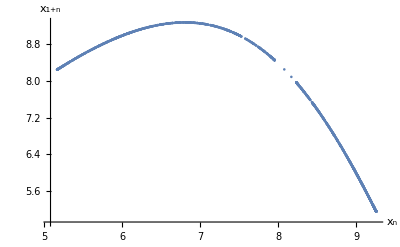

```mathematica
ListPlot[lmap,AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

Reconstrucción del atractor a partir de una sola solución,  (ignorando  y ). Necesitamos definir un tiempo de retraso y graficar la solución original con la solución retrasada una y dos veces.

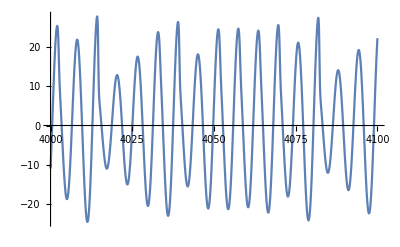

```mathematica
Plot[Evaluate[x[t]/.sol6],{t,4000,4100}]
```

```mathematica
τ=4;
ParametricPlot3D[Evaluate[{x[t],x[t+τ],x[t+2*τ]}/.sol6],{t,0,4500},PlotStyle->{Thick},PlotRange->All,PlotPoints->100,MaxRecursion->10,ColorFunction->Function[{x,y,z,t},ColorData["TemperatureMap"][t]]]
```

-Graphics3D-

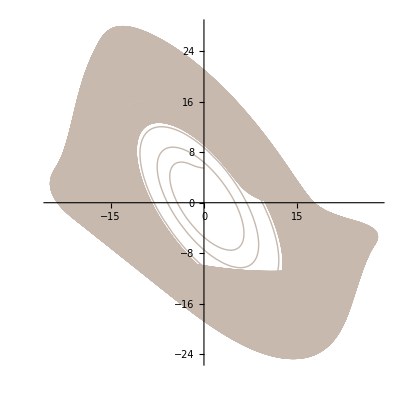

```mathematica
τ=4;
ParametricPlot[Evaluate[{x[t],x[t+τ]}/.sol6],{t,0,4500},PlotStyle->{Thick},PlotRange->All,PlotPoints->100,MaxRecursion->10,ColorFunction->Function[{x,y,t},ColorData["TemperatureMap"][t]]]
```